```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

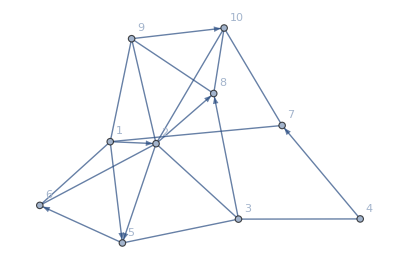

```mathematica
randomMixedGraph=RandomWeightedMixedGraph[{10,20},0.5,RandomReal[]&,VertexLabels->Automatic]
```

```mathematica
MixedGraphToDigraph[randomMixedGraph]
```

-Graphics-

```mathematica
WeightedGraphQ[MixedGraphToDigraph[randomMixedGraph]]
```

True

```mathematica
VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]]
```

{3,5,6,7,9,10}

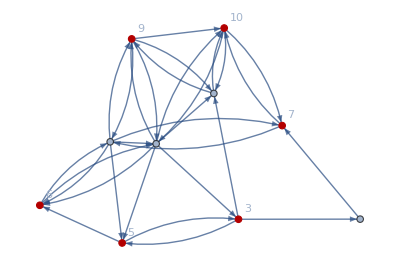

```mathematica
HighlightGraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]
```

```mathematica
VertexDegree[-Graphics-]
```

{8,10,5,2,5,5,5,6,7,7}

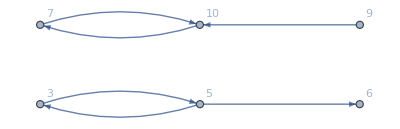

```mathematica
Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]
```

```mathematica
EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]
```

-Graphics-

## Convert to Undirected Graph

```mathematica
EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{1->2,1->5,1->6,1->7,1->9,2->3,2->5,2->6,2->8,2->9,2->10,3->4,3->5,3->5,3->8,4->7,5->3,5->6,5->6,6->1,6->2,7->1,7->10,7->10,8->9,8->10,9->1,9->2,9->8,9->10,9->10,10->2,10->7,10->8}

```mathematica
{First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{{1,2},{1,5},{1,6},{1,7},{1,9},{2,3},{2,5},{2,6},{2,8},{2,9},{2,10},{3,4},{3,5},{3,5},{3,8},{4,7},{5,3},{5,6},{5,6},{6,1},{6,2},{7,1},{7,10},{7,10},{8,9},{8,10},{9,1},{9,2},{9,8},{9,10},{9,10},{10,2},{10,7},{10,8}}

```mathematica
Sort/@{First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[6].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[7].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[9].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[6].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[8].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[9].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[10].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[4].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[8].

Sort::normal: Nonatomic expression expected at position 1 in Sort[4].

Sort::normal: Nonatomic expression expected at position 1 in Sort[7].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[3].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[6].

Sort::normal: Nonatomic expression expected at position 1 in Sort[5].

Sort::normal: Nonatomic expression expected at position 1 in Sort[6].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[6].

Sort::normal: Nonatomic expression expected at position 1 in Sort[2].

Sort::normal: Nonatomic expression expected at position 1 in Sort[7].

Sort::normal: Nonatomic expression expected at position 1 in Sort[1].

Sort::normal: Nonatomic expression expected at position 1 in Sort[7].

Sort::normal: Nonatomic expression expected at position 1 in Sort[10].

Sort::normal: Nonatomic expression expected at position 1 in Sort[7].

Sort::normal: Nonatomic expression expected at position 1 in Sort[10].

## Subgraphs

```mathematica
VertexDegree[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{8,10,6,2,7,6,6,6,8,9}

```mathematica
FindEdgeCover[-Graphics-]
```

{1->9,2->8,3->8,4->7,5->6,9->10}

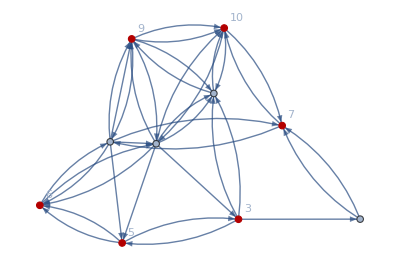

```mathematica
EdgeAdd[-Graphics-,FindEdgeCover[-Graphics-]]
```

```mathematica
VertexDegree[EdgeAdd[-Graphics-,FindEdgeCover[-Graphics-]]]
```

{9,11,6,3,6,6,6,8,9,8}